```mathematica
SetDirectory[NotebookDirectory[]];
w1=Import["A.dat"];
w2=Import["RK_4.dat"];
w3=Import["PC.dat"];
```

```mathematica
(*w4=Import["4.dat"];
w5=Import["5.dat"];
w6=Import["6.dat"];
(*w7=Import["RK_4.dat"];
w8=Import["RK_2.dat"];*)
```

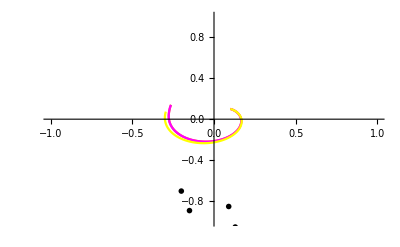

```mathematica
Show[ListLinePlot[{w1},PlotStyle->Directive[Orange]],ListLinePlot[w2,PlotStyle->Directive[Magenta]],ListLinePlot[w3,PlotStyle->Directive[Yellow]],(*ListLinePlot[w4,PlotStyle->Directive[Pink]] ,ListLinePlot[w5,PlotStyle->Directive[Brown]] ,ListLinePlot[w6,PlotStyle->Directive[Lighter@Blue]] ,ListLinePlot[w7,PlotStyle->Directive[Hue[5/4,4/2,1/2]]]  ,ListLinePlot[w8,PlotStyle->Directive[Pink]],*)Graphics[{PointSize[0.01],Point[{0.09,-0.85}], Point[{ 0.13,-1.05}], Point[{ 0.,-1.15}],Point[{ -0.1,-1.1}],Point[{ -0.15,-0.89}],Point[{-0.2,-0.7}],Point[{ -0.05,1.6}],Point[{ 0.0132,1.4}]}], PlotRange->{{-1,1},{-1,1}},BaseStyle->Red]
```

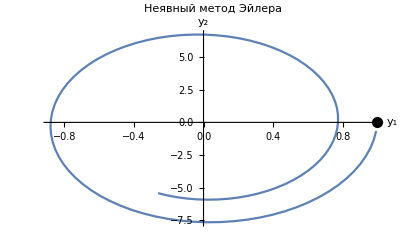

```mathematica
Show[ListLinePlot[w2,AxesLabel->{Subscript[y, 1],Subscript[y, 2]},PlotLabel->"Неявный метод Эйлера"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```

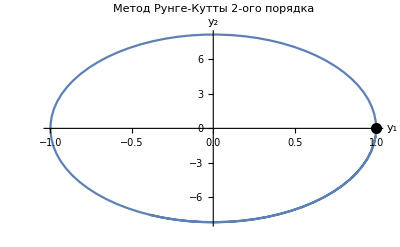

```mathematica
Show[ListLinePlot[w3,AxesLabel->{Subscript[y, 1],Subscript[y, 2]},PlotLabel->"Метод Рунге-Кутты 2-ого порядка"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```

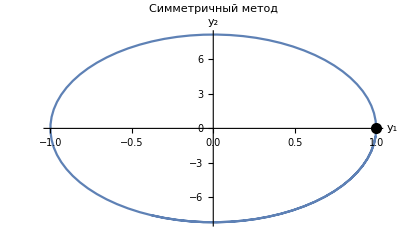

```mathematica
Show[ListLinePlot[w4,AxesLabel->{Subscript[y, 1],Subscript[y, 2]}, PlotLabel->"Симметричный метод"],Graphics[{PointSize[0.02],Point[{1,0}]}]]
```